# Tables of new LHC data

## ATLAS 8 TeV Combination Born

```mathematica
Needs["ErrorBarLogPlots`"]
```

```mathematica
SetDirectory["PhD/newcode/data/DY.newATLAS_original"]
```

/Users/ChiaraBisso/PhD/newcode/data/DY.newATLAS_original

```mathematica
formatExport[x_]:=x//ScientificForm[#,{7,6},NumberFormat->({#1,"e",#3}&)]&//ToString//StringReplace[#,{", }"->", 0}"}]&//ToExpression//Row[{#[[1]]//ScientificForm[#,{7,6},NumberPadding->{"0","0"},SignPadding->True,NumberSigns->{"-","+"}]&,"E",#[[3]]//PaddedForm[#,2,NumberPadding->{"0","0"},SignPadding->True,NumberSigns->{"-","+"}]&}]&;
```

## $0 .0\leq | y_ {\ell\ell} | < 0.4 $

```mathematica
Import["HEPData-ins1408516-v1-Table_17.csv","CSV","HeaderLines"->125]
```

{{1.,0.,2.,0.02704,0.3,-0.3,0.2,-0.2,0.7,-0.7},{3.,2.,4.,0.05569,0.2,-0.2,0.1,-0.1,0.3,-0.3},{5.,4.,6.,0.05571,0.2,-0.2,0.1,-0.1,0.4,-0.4},{7.,6.,8.,0.04883,0.2,-0.2,0.1,-0.1,0.3,-0.3},{9.,8.,10.,0.04086,0.3,-0.3,0.1,-0.1,0.4,-0.4},{11.5,10.,13.,0.03251,0.2,-0.2,0.1,-0.1,0.2,-0.2},{14.5,13.,16.,0.02505,0.3,-0.3,0.1,-0.1,0.2,-0.2},{18.,16.,20.,0.01892,0.2,-0.2,0.1,-0.1,0.2,-0.2},{22.5,20.,25.,0.01365,0.2,-0.2,0.1,-0.1,0.2,-0.2},{27.5,25.,30.,0.009728,0.3,-0.3,0.1,-0.1,0.2,-0.2},{33.5,30.,37.,0.00684,0.3,-0.3,0.1,-0.1,0.2,-0.2},{41.,37.,45.,0.004609,0.3,-0.3,0.1,-0.1,0.2,-0.2},{50.,45.,55.,0.003033,0.3,-0.3,0.1,-0.1,0.3,-0.3},{60.,55.,65.,0.001932,0.4,-0.4,0.2,-0.2,0.4,-0.4},{70.,65.,75.,0.001287,0.5,-0.5,0.2,-0.2,0.4,-0.4},{80.,75.,85.,0.0008569,0.7,-0.7,0.3,-0.3,0.5,-0.5},{95.,85.,105.,0.0004927,0.6,-0.6,0.2,-0.2,0.4,-0.4},{127.5,105.,150.,0.0001884,0.6,-0.6,0.2,-0.2,0.4,-0.4},{175.,150.,200.,0.00005399,1.1,-1.1,0.4,-0.4,0.5,-0.5},{550.,200.,900.,2.284×10^-6,1.4,-1.4,0.4,-0.4,0.8,-0.8}}

```mathematica
table1=Import["HEPData-ins1408516-v1-Table_17.csv","CSV","HeaderLines"->125];
```

```mathematica
Length[table1]
```

20

```mathematica
Take[Import["HEPData-ins1408516-v1-Table_17.csv","CSV","HeaderLines"->123],2]
```

{{#: ,,,$(1/\sigma)\,d\sigma/dp_T^{\ell\ell}$ $\pm$ Statistical [ ] $\pm$ Uncorrelated systematic [ ] $\pm$ Correlated systematic [ ]},{ $p_T^{\ell\ell}$ , $p_T^{\ell\ell}$ LOW , $p_T^{\ell\ell}$ HIGH , Combination Born , stat + , stat - , sys,Uncorrelated + , sys,Uncorrelated - , sys,Correlated + , sys,Correlated -}}

```mathematica
data1=(table1/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,l_}->{a,d,e*d/100,(√((g*d)^2+(i*d)^2))/100})
```

{{1.,0.02704,0.00008112,0.000196854},{3.,0.05569,0.00011138,0.000176107},{5.,0.05571,0.00011142,0.000229698},{7.,0.04883,0.00009766,0.000154414},{9.,0.04086,0.00012258,0.00016847},{11.5,0.03251,0.00006502,0.0000726946},{14.5,0.02505,0.00007515,0.0000560135},{18.,0.01892,0.00003784,0.0000423064},{22.5,0.01365,0.0000273,0.0000305223},{27.5,0.009728,0.000029184,0.0000217525},{33.5,0.00684,0.00002052,0.0000152947},{41.,0.004609,0.000013827,0.000010306},{50.,0.003033,9.099×10^-6,9.59119×10^-6},{60.,0.001932,7.728×10^-6,8.64017×10^-6},{70.,0.001287,6.435×10^-6,5.75564×10^-6},{80.,0.0008569,5.9983×10^-6,4.99654×10^-6},{95.,0.0004927,2.9562×10^-6,2.20342×10^-6},{127.5,0.0001884,1.1304×10^-6,8.4255×10^-7},{175.,0.00005399,5.9389×10^-7,3.45705×10^-7},{550.,2.284×10^-6,3.1976×10^-8,2.04287×10^-8}}

```mathematica
ToPlot1=(data1/.{a_,b_,c_,d_}->{{Log[10,a],Log[10,b]},ErrorBar[{Log[10,(b+√(c^2+d^2))/b]},{Log[10,(b-√(c^2+d^2))/b]}]})
```

{{{0.,-1.56799},ErrorBar[{0.00340625},{-0.00343317}]},{{0.477121,-1.25422},ErrorBar[{0.00162195},{-0.00162803}]},{{0.69897,-1.25407},ErrorBar[{0.00198564},{-0.00199476}]},{{0.845098,-1.31131},ErrorBar[{0.00162195},{-0.00162803}]},{{0.954243,-1.3887},ErrorBar[{0.00220885},{-0.00222014}]},{{1.0607,-1.48798},ErrorBar[{0.00130093},{-0.00130484}]},{{1.16137,-1.60119},ErrorBar[{0.00162195},{-0.00162803}]},{{1.25527,-1.72308},ErrorBar[{0.00130093},{-0.00130484}]},{{1.35218,-1.86487},ErrorBar[{0.00130093},{-0.00130484}]},{{1.43933,-2.01198},ErrorBar[{0.00162195},{-0.00162803}]},{{1.52504,-2.16494},ErrorBar[{0.00162195},{-0.00162803}]},{{1.61278,-2.33639},ErrorBar[{0.00162195},{-0.00162803}]},{{1.69897,-2.51813},ErrorBar[{0.00188893},{-0.00189718}]},{{1.77815,-2.71399},ErrorBar[{0.00259798},{-0.00261362}]},{{1.8451,-2.89042},ErrorBar[{0.00290361},{-0.00292315}]},{{1.90309,-3.06707},ErrorBar[{0.0039387},{-0.00397474}]},{{1.97772,-3.30742},ErrorBar[{0.00323786},{-0.00326218}]},{{2.10551,-3.72492},ErrorBar[{0.00323786},{-0.00326218}]},{{2.24304,-4.26769},ErrorBar[{0.00549278},{-0.00556315}]},{{2.74036,-5.6413},ErrorBar[{0.00715576},{-0.00727565}]}}

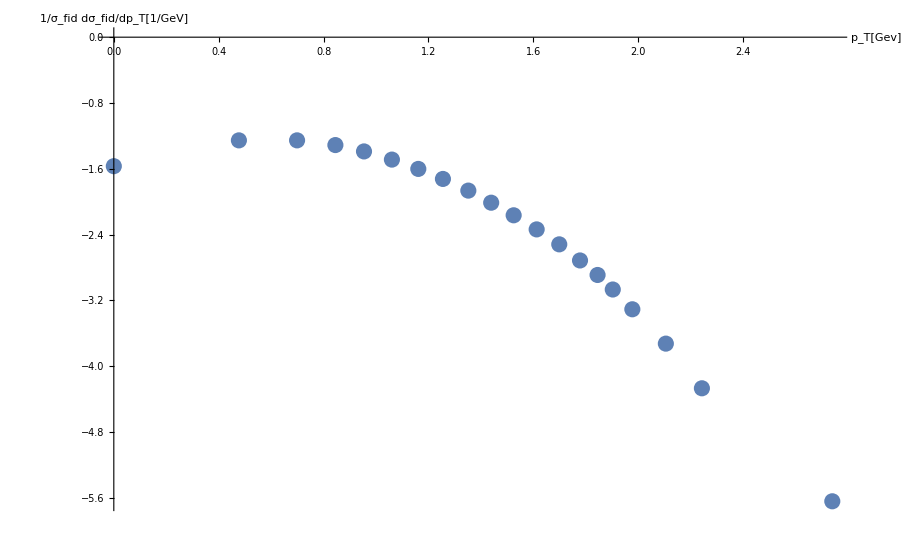

```mathematica
ErrorListPlot[ToPlot1,AxesLabel->{"p_T[Gev]", "1/σ_fid dσ_fid/dp_T[1/GeV]"},PlotRange -> All, LabelStyle->Directive[Black,FontFamily->"Helvetica",10]]
```

```mathematica
data1Export= Table[formatExport[data1[[k,i]]]//ToString,{k,1,20},{i,1,4}]
```

{{+1.000000E+00,+2.704000E-02,+8.112000E-05,+1.968542E-04},{+3.000000E+00,+5.569000E-02,+1.113800E-04,+1.761072E-04},{+5.000000E+00,+5.571000E-02,+1.114200E-04,+2.296982E-04},{+7.000000E+00,+4.883000E-02,+9.766000E-05,+1.544140E-04},{+9.000000E+00,+4.086000E-02,+1.225800E-04,+1.684701E-04},{+1.150000E+01,+3.251000E-02,+6.502000E-05,+7.269457E-05},{+1.450000E+01,+2.505000E-02,+7.515000E-05,+5.601350E-05},{+1.800000E+01,+1.892000E-02,+3.784000E-05,+4.230641E-05},{+2.250000E+01,+1.365000E-02,+2.730000E-05,+3.052233E-05},{+2.750000E+01,+9.728000E-03,+2.918400E-05,+2.175247E-05},{+3.350000E+01,+6.840000E-03,+2.052000E-05,+1.529470E-05},{+4.100000E+01,+4.609000E-03,+1.382700E-05,+1.030604E-05},{+5.000000E+01,+3.033000E-03,+9.099000E-06,+9.591188E-06},{+6.000000E+01,+1.932000E-03,+7.728000E-06,+8.640167E-06},{+7.000000E+01,+1.287000E-03,+6.435000E-06,+5.755639E-06},{+8.000000E+01,+8.569000E-04,+5.998300E-06,+4.996543E-06},{+9.500000E+01,+4.927000E-04,+2.956200E-06,+2.203421E-06},{+1.275000E+02,+1.884000E-04,+1.130400E-06,+8.425504E-07},{+1.750000E+02,+5.399000E-05,+5.938900E-07,+3.457047E-07},{+5.500000E+02,+2.284000E-06,+3.197600E-08,+2.042872E-08}}

```mathematica
(*Export["DY.newATLAS_8TeV_yrap0_0.4.list",data1Export,"table"]*)
```

## # : $ 0.4 \leq |y_{\ell\ell}| < 0.8$

```mathematica
table2=Import["HEPData-ins1408516-v1-Table_18.csv","CSV","HeaderLines"->125]
```

{{1.,0.,2.,0.0269,0.3,-0.3,0.2,-0.2,0.8,-0.8},{3.,2.,4.,0.05575,0.2,-0.2,0.1,-0.1,0.3,-0.3},{5.,4.,6.,0.05642,0.2,-0.2,0.1,-0.1,0.3,-0.3},{7.,6.,8.,0.04922,0.3,-0.3,0.1,-0.1,0.4,-0.4},{9.,8.,10.,0.04071,0.3,-0.3,0.1,-0.1,0.4,-0.4},{11.5,10.,13.,0.03256,0.2,-0.2,0.1,-0.1,0.2,-0.2},{14.5,13.,16.,0.02501,0.3,-0.3,0.1,-0.1,0.2,-0.2},{18.,16.,20.,0.01894,0.3,-0.3,0.1,-0.1,0.2,-0.2},{22.5,20.,25.,0.01359,0.3,-0.3,0.1,-0.1,0.2,-0.2},{27.5,25.,30.,0.009719,0.3,-0.3,0.1,-0.1,0.2,-0.2},{33.5,30.,37.,0.006763,0.3,-0.3,0.1,-0.1,0.2,-0.2},{41.,37.,45.,0.004589,0.3,-0.3,0.1,-0.1,0.3,-0.3},{50.,45.,55.,0.002984,0.4,-0.4,0.1,-0.1,0.3,-0.3},{60.,55.,65.,0.001926,0.4,-0.4,0.2,-0.2,0.4,-0.4},{70.,65.,75.,0.001283,0.6,-0.6,0.2,-0.2,0.5,-0.5},{80.,75.,85.,0.0008633,0.7,-0.7,0.3,-0.3,0.5,-0.5},{95.,85.,105.,0.0004858,0.6,-0.6,0.2,-0.2,0.5,-0.5},{127.5,105.,150.,0.0001874,0.6,-0.6,0.2,-0.2,0.5,-0.5},{175.,150.,200.,0.00005303,1.1,-1.1,0.4,-0.4,0.7,-0.7},{550.,200.,900.,2.145×10^-6,1.4,-1.4,0.4,-0.4,1.,-1.}}

```mathematica
Take[Import["HEPData-ins1408516-v1-Table_18.csv","CSV","HeaderLines"->123],2]
```

{{#: ,,,$(1/\sigma)\,d\sigma/dp_T^{\ell\ell}$ $\pm$ Statistical [ ] $\pm$ Uncorrelated systematic [ ] $\pm$ Correlated systematic [ ]},{ $p_T^{\ell\ell}$ , $p_T^{\ell\ell}$ LOW , $p_T^{\ell\ell}$ HIGH , Combination Born , stat + , stat - , sys,Uncorrelated + , sys,Uncorrelated - , sys,Correlated + , sys,Correlated -}}

```mathematica
data2=(table2/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,l_}->{a,d,e*d/100,(√((g*d)^2+(i*d)^2))/100})
```

{{1.,0.0269,0.0000807,0.000221823},{3.,0.05575,0.0001115,0.000176297},{5.,0.05642,0.00011284,0.000178416},{7.,0.04922,0.00014766,0.000202939},{9.,0.04071,0.00012213,0.000167852},{11.5,0.03256,0.00006512,0.0000728064},{14.5,0.02501,0.00007503,0.0000559241},{18.,0.01894,0.00005682,0.0000423511},{22.5,0.01359,0.00004077,0.0000303882},{27.5,0.009719,0.000029157,0.0000217323},{33.5,0.006763,0.000020289,0.0000151225},{41.,0.004589,0.000013767,0.0000145117},{50.,0.002984,0.000011936,9.43624×10^-6},{60.,0.001926,7.704×10^-6,8.61333×10^-6},{70.,0.001283,7.698×10^-6,6.90917×10^-6},{80.,0.0008633,6.0431×10^-6,5.03386×10^-6},{95.,0.0004858,2.9148×10^-6,2.61611×10^-6},{127.5,0.0001874,1.1244×10^-6,1.00918×10^-6},{175.,0.00005303,5.8333×10^-7,4.27542×10^-7},{550.,2.145×10^-6,3.003×10^-8,2.31024×10^-8}}

```mathematica
ToPlot2=(data2/.{a_,b_,c_,d_}->{{Log[10,a],Log[10,b]},ErrorBar[{Log[10,(b+√(c^2+d^2))/b]},{Log[10,(b-√(c^2+d^2))/b]}]})
```

{{{0.,-1.57025},ErrorBar[{0.0037943},{-0.00382774}]},{{0.477121,-1.25376},ErrorBar[{0.00162195},{-0.00162803}]},{{0.69897,-1.24857},ErrorBar[{0.00162195},{-0.00162803}]},{{0.845098,-1.30786},ErrorBar[{0.00220885},{-0.00222014}]},{{0.954243,-1.3903},ErrorBar[{0.00220885},{-0.00222014}]},{{1.0607,-1.48732},ErrorBar[{0.00130093},{-0.00130484}]},{{1.16137,-1.60189},ErrorBar[{0.00162195},{-0.00162803}]},{{1.25527,-1.72262},ErrorBar[{0.00162195},{-0.00162803}]},{{1.35218,-1.86678},ErrorBar[{0.00162195},{-0.00162803}]},{{1.43933,-2.01238},ErrorBar[{0.00162195},{-0.00162803}]},{{1.52504,-2.16986},ErrorBar[{0.00162195},{-0.00162803}]},{{1.61278,-2.33828},ErrorBar[{0.00188893},{-0.00189718}]},{{1.69897,-2.5252},ErrorBar[{0.00220885},{-0.00222014}]},{{1.77815,-2.71534},ErrorBar[{0.00259798},{-0.00261362}]},{{1.8451,-2.89177},ErrorBar[{0.00348735},{-0.00351558}]},{{1.90309,-3.06384},ErrorBar[{0.0039387},{-0.00397474}]},{{1.97772,-3.31354},ErrorBar[{0.00348735},{-0.00351558}]},{{2.10551,-3.72723},ErrorBar[{0.00348735},{-0.00351558}]},{{2.24304,-4.27548},ErrorBar[{0.00588296},{-0.00596375}]},{{2.74036,-5.66857},ErrorBar[{0.00760421},{-0.00773973}]}}

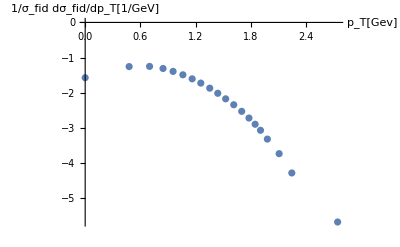

```mathematica
ErrorListPlot[ToPlot2,AxesLabel->{"p_T[Gev]", "1/σ_fid dσ_fid/dp_T[1/GeV]"},PlotRange -> All, LabelStyle->Directive[Black,FontFamily->"Helvetica",10]]
```

```mathematica
data2Export= Table[formatExport[data2[[k,i]]]//ToString,{k,1,20},{i,1,4}]
```

{{+1.000000E+00,+2.690000E-02,+8.070000E-05,+2.218231E-04},{+3.000000E+00,+5.575000E-02,+1.115000E-04,+1.762970E-04},{+5.000000E+00,+5.642000E-02,+1.128400E-04,+1.784157E-04},{+7.000000E+00,+4.922000E-02,+1.476600E-04,+2.029393E-04},{+9.000000E+00,+4.071000E-02,+1.221300E-04,+1.678516E-04},{+1.150000E+01,+3.256000E-02,+6.512000E-05,+7.280637E-05},{+1.450000E+01,+2.501000E-02,+7.503000E-05,+5.592406E-05},{+1.800000E+01,+1.894000E-02,+5.682000E-05,+4.235113E-05},{+2.250000E+01,+1.359000E-02,+4.077000E-05,+3.038816E-05},{+2.750000E+01,+9.719000E-03,+2.915700E-05,+2.173234E-05},{+3.350000E+01,+6.763000E-03,+2.028900E-05,+1.512253E-05},{+4.100000E+01,+4.589000E-03,+1.376700E-05,+1.451169E-05},{+5.000000E+01,+2.984000E-03,+1.193600E-05,+9.436237E-06},{+6.000000E+01,+1.926000E-03,+7.704000E-06,+8.613334E-06},{+7.000000E+01,+1.283000E-03,+7.698000E-06,+6.909166E-06},{+8.000000E+01,+8.633000E-04,+6.043100E-06,+5.033861E-06},{+9.500000E+01,+4.858000E-04,+2.914800E-06,+2.616113E-06},{+1.275000E+02,+1.874000E-04,+1.124400E-06,+1.009180E-06},{+1.750000E+02,+5.303000E-05,+5.833300E-07,+4.275415E-07},{+5.500000E+02,+2.145000E-06,+3.003000E-08,+2.310236E-08}}

```mathematica
(*Export["DY.newATLAS_8TeV_yrap0.4_0.8.list",data2Export,"table"]*)
```

## # : $ 0.8 \leq |y_{\ell\ell}| < 1.2$

```mathematica
table3=Import["HEPData-ins1408516-v1-Table_19.csv","CSV","HeaderLines"->125]
```

{{1.,0.,2.,0.02711,0.4,-0.4,0.2,-0.2,0.6,-0.6},{3.,2.,4.,0.05611,0.2,-0.2,0.1,-0.1,0.3,-0.3},{5.,4.,6.,0.05691,0.2,-0.2,0.1,-0.1,0.3,-0.3},{7.,6.,8.,0.04906,0.3,-0.3,0.1,-0.1,0.3,-0.3},{9.,8.,10.,0.04096,0.3,-0.3,0.1,-0.1,0.4,-0.4},{11.5,10.,13.,0.03244,0.3,-0.3,0.1,-0.1,0.3,-0.3},{14.5,13.,16.,0.02519,0.3,-0.3,0.1,-0.1,0.2,-0.2},{18.,16.,20.,0.01888,0.3,-0.3,0.1,-0.1,0.2,-0.2},{22.5,20.,25.,0.01355,0.3,-0.3,0.1,-0.1,0.2,-0.2},{27.5,25.,30.,0.009693,0.3,-0.3,0.1,-0.1,0.2,-0.2},{33.5,30.,37.,0.006777,0.3,-0.3,0.1,-0.1,0.2,-0.2},{41.,37.,45.,0.004544,0.3,-0.3,0.1,-0.1,0.3,-0.3},{50.,45.,55.,0.00294,0.4,-0.4,0.2,-0.2,0.3,-0.3},{60.,55.,65.,0.001907,0.5,-0.5,0.2,-0.2,0.5,-0.5},{70.,65.,75.,0.001249,0.6,-0.6,0.2,-0.2,0.5,-0.5},{80.,75.,85.,0.0008337,0.7,-0.7,0.3,-0.3,0.5,-0.5},{95.,85.,105.,0.0004832,0.6,-0.6,0.2,-0.2,0.4,-0.4},{127.5,105.,150.,0.0001831,0.6,-0.6,0.3,-0.3,0.5,-0.5},{175.,150.,200.,0.00005182,1.2,-1.2,0.4,-0.4,0.7,-0.7},{550.,200.,900.,2.061×10^-6,1.5,-1.5,0.5,-0.5,0.9,-0.9}}

```mathematica
Take[Import["HEPData-ins1408516-v1-Table_19.csv","CSV","HeaderLines"->123],2]
```

{{#: ,,,$(1/\sigma)\,d\sigma/dp_T^{\ell\ell}$ $\pm$ Statistical [ ] $\pm$ Uncorrelated systematic [ ] $\pm$ Correlated systematic [ ]},{ $p_T^{\ell\ell}$ , $p_T^{\ell\ell}$ LOW , $p_T^{\ell\ell}$ HIGH , Combination Born , stat + , stat - , sys,Uncorrelated + , sys,Uncorrelated - , sys,Correlated + , sys,Correlated -}}

```mathematica
data3=(table3/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,l_}->{a,d,e*d/100,(√((g*d)^2+(i*d)^2))/100})
```

{{1.,0.02711,0.00010844,0.000171459},{3.,0.05611,0.00011222,0.000177435},{5.,0.05691,0.00011382,0.000179965},{7.,0.04906,0.00014718,0.000155141},{9.,0.04096,0.00012288,0.000168882},{11.5,0.03244,0.00009732,0.000102584},{14.5,0.02519,0.00007557,0.0000563266},{18.,0.01888,0.00005664,0.000042217},{22.5,0.01355,0.00004065,0.0000302987},{27.5,0.009693,0.000029079,0.0000216742},{33.5,0.006777,0.000020331,0.0000151538},{41.,0.004544,0.000013632,0.0000143694},{50.,0.00294,0.00001176,0.0000106003},{60.,0.001907,9.535×10^-6,0.0000102695},{70.,0.001249,7.494×10^-6,6.72607×10^-6},{80.,0.0008337,5.8359×10^-6,4.86126×10^-6},{95.,0.0004832,2.8992×10^-6,2.16094×10^-6},{127.5,0.0001831,1.0986×10^-6,1.06765×10^-6},{175.,0.00005182,6.2184×10^-7,4.17786×10^-7},{550.,2.061×10^-6,3.0915×10^-8,2.12193×10^-8}}

```mathematica
ToPlot3=(data3/.{a_,b_,c_,d_}->{{Log[10,a],Log[10,b]},ErrorBar[{Log[10,(b+√(c^2+d^2))/b]},{Log[10,(b-√(c^2+d^2))/b]}]})
```

{{{0.,-1.56687},ErrorBar[{0.00323786},{-0.00326218}]},{{0.477121,-1.25096},ErrorBar[{0.00162195},{-0.00162803}]},{{0.69897,-1.24481},ErrorBar[{0.00162195},{-0.00162803}]},{{0.845098,-1.30927},ErrorBar[{0.00188893},{-0.00189718}]},{{0.954243,-1.38764},ErrorBar[{0.00220885},{-0.00222014}]},{{1.0607,-1.48892},ErrorBar[{0.00188893},{-0.00189718}]},{{1.16137,-1.59877},ErrorBar[{0.00162195},{-0.00162803}]},{{1.25527,-1.724},ErrorBar[{0.00162195},{-0.00162803}]},{{1.35218,-1.86806},ErrorBar[{0.00162195},{-0.00162803}]},{{1.43933,-2.01354},ErrorBar[{0.00162195},{-0.00162803}]},{{1.52504,-2.16896},ErrorBar[{0.00162195},{-0.00162803}]},{{1.61278,-2.34256},ErrorBar[{0.00188893},{-0.00189718}]},{{1.69897,-2.53165},ErrorBar[{0.00233247},{-0.00234507}]},{{1.77815,-2.71965},ErrorBar[{0.00317973},{-0.00320318}]},{{1.8451,-2.90344},ErrorBar[{0.00348735},{-0.00351558}]},{{1.90309,-3.07899},ErrorBar[{0.0039387},{-0.00397474}]},{{1.97772,-3.31587},ErrorBar[{0.00323786},{-0.00326218}]},{{2.10551,-3.73731},ErrorBar[{0.00361845},{-0.00364885}]},{{2.24304,-4.2855},ErrorBar[{0.00623357},{-0.00632435}]},{{2.74036,-5.68592},ErrorBar[{0.00783028},{-0.00797406}]}}

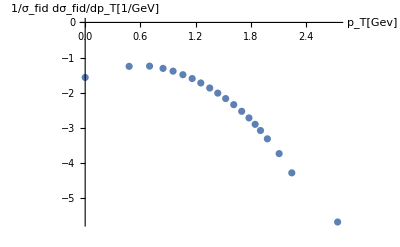

```mathematica
ErrorListPlot[ToPlot3,AxesLabel->{"p_T[Gev]", "1/σ_fid dσ_fid/dp_T[1/GeV]"},PlotRange -> All, LabelStyle->Directive[Black,FontFamily->"Helvetica",10]]
```

```mathematica
data3Export= Table[formatExport[data3[[k,i]]]//ToString,{k,1,20},{i,1,4}]
```

{{+1.000000E+00,+2.711000E-02,+1.084400E-04,+1.714587E-04},{+3.000000E+00,+5.611000E-02,+1.122200E-04,+1.774354E-04},{+5.000000E+00,+5.691000E-02,+1.138200E-04,+1.799652E-04},{+7.000000E+00,+4.906000E-02,+1.471800E-04,+1.551413E-04},{+9.000000E+00,+4.096000E-02,+1.228800E-04,+1.688824E-04},{+1.150000E+01,+3.244000E-02,+9.732000E-05,+1.025843E-04},{+1.450000E+01,+2.519000E-02,+7.557000E-05,+5.632655E-05},{+1.800000E+01,+1.888000E-02,+5.664000E-05,+4.221696E-05},{+2.250000E+01,+1.355000E-02,+4.065000E-05,+3.029872E-05},{+2.750000E+01,+9.693000E-03,+2.907900E-05,+2.167421E-05},{+3.350000E+01,+6.777000E-03,+2.033100E-05,+1.515383E-05},{+4.100000E+01,+4.544000E-03,+1.363200E-05,+1.436939E-05},{+5.000000E+01,+2.940000E-03,+1.176000E-05,+1.060032E-05},{+6.000000E+01,+1.907000E-03,+9.535000E-06,+1.026951E-05},{+7.000000E+01,+1.249000E-03,+7.494000E-06,+6.726071E-06},{+8.000000E+01,+8.337000E-04,+5.835900E-06,+4.861265E-06},{+9.500000E+01,+4.832000E-04,+2.899200E-06,+2.160936E-06},{+1.275000E+02,+1.831000E-04,+1.098600E-06,+1.067647E-06},{+1.750000E+02,+5.182000E-05,+6.218400E-07,+4.177862E-07},{+5.500000E+02,+2.061000E-06,+3.091500E-08,+2.121929E-08}}

```mathematica
(*Export["DY.newATLAS_8TeV_yrap0.8_1.2.list",data3Export,"table"]*)
```

## # : $1.2 \leq |y_{\ell\ell}| < 1.6$

```mathematica
table4=Import["HEPData-ins1408516-v1-Table_20.csv","CSV","HeaderLines"->125]
```

{{1.,0.,2.,0.02658,0.4,-0.4,0.2,-0.2,0.7,-0.7},{3.,2.,4.,0.05536,0.3,-0.3,0.1,-0.1,0.4,-0.4},{5.,4.,6.,0.05529,0.3,-0.3,0.2,-0.2,0.4,-0.4},{7.,6.,8.,0.04816,0.3,-0.3,0.1,-0.1,0.5,-0.5},{9.,8.,10.,0.04066,0.3,-0.3,0.2,-0.2,0.5,-0.5},{11.5,10.,13.,0.0327,0.3,-0.3,0.1,-0.1,0.3,-0.3},{14.5,13.,16.,0.02534,0.3,-0.3,0.1,-0.1,0.2,-0.2},{18.,16.,20.,0.01917,0.3,-0.3,0.1,-0.1,0.2,-0.2},{22.5,20.,25.,0.01374,0.3,-0.3,0.1,-0.1,0.2,-0.2},{27.5,25.,30.,0.009915,0.4,-0.4,0.1,-0.1,0.3,-0.3},{33.5,30.,37.,0.006918,0.4,-0.4,0.1,-0.1,0.2,-0.2},{41.,37.,45.,0.004606,0.4,-0.4,0.2,-0.2,0.3,-0.3},{50.,45.,55.,0.002978,0.4,-0.4,0.2,-0.2,0.3,-0.3},{60.,55.,65.,0.001939,0.5,-0.5,0.2,-0.2,0.4,-0.4},{70.,65.,75.,0.001284,0.7,-0.7,0.3,-0.3,0.5,-0.5},{80.,75.,85.,0.0008786,0.8,-0.8,0.3,-0.3,0.5,-0.5},{95.,85.,105.,0.0004959,0.7,-0.7,0.3,-0.3,0.5,-0.5},{127.5,105.,150.,0.0001936,0.7,-0.7,0.2,-0.2,0.5,-0.5},{175.,150.,200.,0.00005363,1.3,-1.3,0.4,-0.4,0.7,-0.7},{550.,200.,900.,2.099×10^-6,1.7,-1.7,0.5,-0.5,1.1,-1.1}}

```mathematica
Take[Import["HEPData-ins1408516-v1-Table_20.csv","CSV","HeaderLines"->123],2]
```

{{#: ,,,$(1/\sigma)\,d\sigma/dp_T^{\ell\ell}$ $\pm$ Statistical [ ] $\pm$ Uncorrelated systematic [ ] $\pm$ Correlated systematic [ ]},{ $p_T^{\ell\ell}$ , $p_T^{\ell\ell}$ LOW , $p_T^{\ell\ell}$ HIGH , Combination Born , stat + , stat - , sys,Uncorrelated + , sys,Uncorrelated - , sys,Correlated + , sys,Correlated -}}

```mathematica
data4=(table4/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,l_}->{a,d,e*d/100,(√((g*d)^2+(i*d)^2))/100})
```

{{1.,0.02658,0.00010632,0.000193505},{3.,0.05536,0.00016608,0.000228255},{5.,0.05529,0.00016587,0.000247264},{7.,0.04816,0.00014448,0.000245569},{9.,0.04066,0.00012198,0.000218961},{11.5,0.0327,0.0000981,0.000103406},{14.5,0.02534,0.00007602,0.000056662},{18.,0.01917,0.00005751,0.0000428654},{22.5,0.01374,0.00004122,0.0000307236},{27.5,0.009915,0.00003966,0.000031354},{33.5,0.006918,0.000027672,0.0000154691},{41.,0.004606,0.000018424,0.0000166072},{50.,0.002978,0.000011912,0.0000107373},{60.,0.001939,9.695×10^-6,8.67147×10^-6},{70.,0.001284,8.988×10^-6,7.48694×10^-6},{80.,0.0008786,7.0288×10^-6,5.12307×10^-6},{95.,0.0004959,3.4713×10^-6,2.89157×10^-6},{127.5,0.0001936,1.3552×10^-6,1.04257×10^-6},{175.,0.00005363,6.9719×10^-7,4.32379×10^-7},{550.,2.099×10^-6,3.5683×10^-8,2.53623×10^-8}}

```mathematica
ToPlot4=(data4/.{a_,b_,c_,d_}->{{Log[10,a],Log[10,b]},ErrorBar[{Log[10,(b+√(c^2+d^2))/b]},{Log[10,(b-√(c^2+d^2))/b]}]})
```

{{{0.,-1.57545},ErrorBar[{0.00359262},{-0.00362259}]},{{0.477121,-1.2568},ErrorBar[{0.00220885},{-0.00222014}]},{{0.69897,-1.25735},ErrorBar[{0.00233247},{-0.00234507}]},{{0.845098,-1.31731},ErrorBar[{0.00256175},{-0.00257695}]},{{0.954243,-1.39083},ErrorBar[{0.00266895},{-0.00268546}]},{{1.0607,-1.48545},ErrorBar[{0.00188893},{-0.00189718}]},{{1.16137,-1.59619},ErrorBar[{0.00162195},{-0.00162803}]},{{1.25527,-1.71738},ErrorBar[{0.00162195},{-0.00162803}]},{{1.35218,-1.86201},ErrorBar[{0.00162195},{-0.00162803}]},{{1.43933,-2.00371},ErrorBar[{0.00220885},{-0.00222014}]},{{1.52504,-2.16002},ErrorBar[{0.00198564},{-0.00199476}]},{{1.61278,-2.33668},ErrorBar[{0.00233247},{-0.00234507}]},{{1.69897,-2.52608},ErrorBar[{0.00233247},{-0.00234507}]},{{1.77815,-2.71242},ErrorBar[{0.00290361},{-0.00292315}]},{{1.8451,-2.89143},ErrorBar[{0.0039387},{-0.00397474}]},{{1.90309,-3.05621},ErrorBar[{0.00427816},{-0.00432072}]},{{1.97772,-3.30461},ErrorBar[{0.0039387},{-0.00397474}]},{{2.10551,-3.71309},ErrorBar[{0.00381875},{-0.00385262}]},{{2.24304,-4.27059},ErrorBar[{0.00659313},{-0.00669476}]},{{2.74036,-5.67799},ErrorBar[{0.00896476},{-0.00915372}]}}

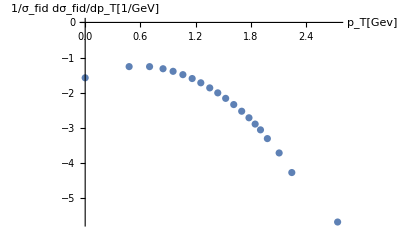

```mathematica
ErrorListPlot[ToPlot4,AxesLabel->{"p_T[Gev]", "1/σ_fid dσ_fid/dp_T[1/GeV]"},PlotRange -> All, LabelStyle->Directive[Black,FontFamily->"Helvetica",10]]
```

```mathematica
data4Export= Table[formatExport[data4[[k,i]]]//ToString,{k,1,20},{i,1,4}]
```

{{+1.000000E+00,+2.658000E-02,+1.063200E-04,+1.935053E-04},{+3.000000E+00,+5.536000E-02,+1.660800E-04,+2.282551E-04},{+5.000000E+00,+5.529000E-02,+1.658700E-04,+2.472644E-04},{+7.000000E+00,+4.816000E-02,+1.444800E-04,+2.455688E-04},{+9.000000E+00,+4.066000E-02,+1.219800E-04,+2.189608E-04},{+1.150000E+01,+3.270000E-02,+9.810000E-05,+1.034065E-04},{+1.450000E+01,+2.534000E-02,+7.602000E-05,+5.666196E-05},{+1.800000E+01,+1.917000E-02,+5.751000E-05,+4.286542E-05},{+2.250000E+01,+1.374000E-02,+4.122000E-05,+3.072357E-05},{+2.750000E+01,+9.915000E-03,+3.966000E-05,+3.135398E-05},{+3.350000E+01,+6.918000E-03,+2.767200E-05,+1.546912E-05},{+4.100000E+01,+4.606000E-03,+1.842400E-05,+1.660717E-05},{+5.000000E+01,+2.978000E-03,+1.191200E-05,+1.073733E-05},{+6.000000E+01,+1.939000E-03,+9.695000E-06,+8.671472E-06},{+7.000000E+01,+1.284000E-03,+8.988000E-06,+7.486942E-06},{+8.000000E+01,+8.786000E-04,+7.028800E-06,+5.123074E-06},{+9.500000E+01,+4.959000E-04,+3.471300E-06,+2.891569E-06},{+1.275000E+02,+1.936000E-04,+1.355200E-06,+1.042568E-06},{+1.750000E+02,+5.363000E-05,+6.971900E-07,+4.323789E-07},{+5.500000E+02,+2.099000E-06,+3.568300E-08,+2.536231E-08}}

```mathematica
(*Export["DY.newATLAS_8TeV_yrap1.2_1.6.list",data4Export,"table"]*)
```

## # : $1.6 \leq |y_{\ell\ell}| < 2.0$

```mathematica
table5=Import["HEPData-ins1408516-v1-Table_21.csv","CSV","HeaderLines"->125]
```

{{1.,0.,2.,0.02606,0.5,-0.5,0.3,-0.3,0.9,-0.9},{3.,2.,4.,0.05394,0.3,-0.3,0.2,-0.2,0.6,-0.6},{5.,4.,6.,0.05425,0.3,-0.3,0.2,-0.2,0.4,-0.4},{7.,6.,8.,0.04667,0.3,-0.3,0.2,-0.2,0.6,-0.6},{9.,8.,10.,0.03925,0.4,-0.4,0.2,-0.2,0.4,-0.4},{11.5,10.,13.,0.0318,0.3,-0.3,0.2,-0.2,0.2,-0.2},{14.5,13.,16.,0.02489,0.4,-0.4,0.2,-0.2,0.3,-0.3},{18.,16.,20.,0.01914,0.4,-0.4,0.2,-0.2,0.3,-0.3},{22.5,20.,25.,0.01403,0.4,-0.4,0.2,-0.2,0.3,-0.3},{27.5,25.,30.,0.01025,0.5,-0.5,0.2,-0.2,0.4,-0.4},{33.5,30.,37.,0.007398,0.4,-0.4,0.2,-0.2,0.3,-0.3},{41.,37.,45.,0.004994,0.5,-0.5,0.2,-0.2,0.4,-0.4},{50.,45.,55.,0.003241,0.5,-0.5,0.2,-0.2,0.4,-0.4},{60.,55.,65.,0.002052,0.7,-0.7,0.3,-0.3,0.6,-0.6},{70.,65.,75.,0.001349,0.8,-0.8,0.4,-0.4,0.6,-0.6},{80.,75.,85.,0.0009165,1.,-1.,0.4,-0.4,0.8,-0.8},{95.,85.,105.,0.000529,0.8,-0.8,0.4,-0.4,0.6,-0.6},{127.5,105.,150.,0.0002056,0.8,-0.8,0.3,-0.3,0.5,-0.5},{175.,150.,200.,0.00006014,1.5,-1.5,0.5,-0.5,0.8,-0.8},{550.,200.,900.,2.06×10^-6,2.1,-2.1,0.7,-0.7,1.3,-1.3}}

```mathematica
Take[Import["HEPData-ins1408516-v1-Table_21.csv","CSV","HeaderLines"->123],2]
```

{{#: ,,,$(1/\sigma)\,d\sigma/dp_T^{\ell\ell}$ $\pm$ Statistical [ ] $\pm$ Uncorrelated systematic [ ] $\pm$ Correlated systematic [ ]},{ $p_T^{\ell\ell}$ , $p_T^{\ell\ell}$ LOW , $p_T^{\ell\ell}$ HIGH , Combination Born , stat + , stat - , sys,Uncorrelated + , sys,Uncorrelated - , sys,Correlated + , sys,Correlated -}}

```mathematica
data5=(table5/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,l_}->{a,d,e*d/100,(√((g*d)^2+(i*d)^2))/100})
```

{{1.,0.02606,0.0001303,0.000247227},{3.,0.05394,0.00016182,0.000341147},{5.,0.05425,0.00016275,0.000242613},{7.,0.04667,0.00014001,0.000295167},{9.,0.03925,0.000157,0.000175531},{11.5,0.0318,0.0000954,0.000089944},{14.5,0.02489,0.00009956,0.0000897422},{18.,0.01914,0.00007656,0.0000690103},{22.5,0.01403,0.00005612,0.0000505859},{27.5,0.01025,0.00005125,0.0000458394},{33.5,0.007398,0.000029592,0.0000266739},{41.,0.004994,0.00002497,0.0000223338},{50.,0.003241,0.000016205,0.0000144942},{60.,0.002052,0.000014364,0.0000137652},{70.,0.001349,0.000010792,9.72778×10^-6},{80.,0.0009165,9.165×10^-6,8.19743×10^-6},{95.,0.000529,4.232×10^-6,3.81467×10^-6},{127.5,0.0002056,1.6448×10^-6,1.19884×10^-6},{175.,0.00006014,9.021×10^-7,5.6736×10^-7},{550.,2.06×10^-6,4.326×10^-8,3.04155×10^-8}}

```mathematica
ToPlot5=(data5/.{a_,b_,c_,d_}->{{Log[10,a],Log[10,b]},ErrorBar[{Log[10,(b+√(c^2+d^2))/b]},{Log[10,(b-√(c^2+d^2))/b]}]})
```

{{{0.,-1.58403},ErrorBar[{0.00463249},{-0.00468244}]},{{0.477121,-1.26809},ErrorBar[{0.00302947},{-0.00305075}]},{{0.69897,-1.2656},ErrorBar[{0.00233247},{-0.00234507}]},{{0.845098,-1.33096},ErrorBar[{0.00302947},{-0.00305075}]},{{0.954243,-1.40616},ErrorBar[{0.00259798},{-0.00261362}]},{{1.0607,-1.49757},ErrorBar[{0.00178696},{-0.00179434}]},{{1.16137,-1.60398},ErrorBar[{0.00233247},{-0.00234507}]},{{1.25527,-1.71806},ErrorBar[{0.00233247},{-0.00234507}]},{{1.35218,-1.85294},ErrorBar[{0.00233247},{-0.00234507}]},{{1.43933,-1.98928},ErrorBar[{0.00290361},{-0.00292315}]},{{1.52504,-2.13089},ErrorBar[{0.00233247},{-0.00234507}]},{{1.61278,-2.30155},ErrorBar[{0.00290361},{-0.00292315}]},{{1.69897,-2.48932},ErrorBar[{0.00290361},{-0.00292315}]},{{1.77815,-2.68782},ErrorBar[{0.00419036},{-0.00423119}]},{{1.8451,-2.86999},ErrorBar[{0.00465249},{-0.00470287}]},{{1.90309,-3.03787},ErrorBar[{0.00578793},{-0.00586611}]},{{1.97772,-3.27654},ErrorBar[{0.00465249},{-0.00470287}]},{{2.10551,-3.68698},ErrorBar[{0.00427816},{-0.00432072}]},{{2.24304,-4.22084},ErrorBar[{0.00762833},{-0.00776472}]},{{2.74036,-5.68613},ErrorBar[{0.0110081},{-0.0112944}]}}

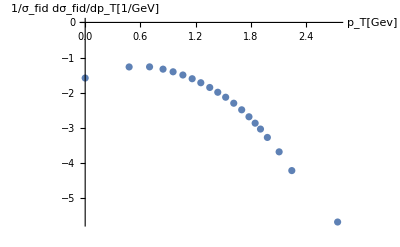

```mathematica
ErrorListPlot[ToPlot5,AxesLabel->{"p_T[Gev]", "1/σ_fid dσ_fid/dp_T[1/GeV]"},PlotRange -> All, LabelStyle->Directive[Black,FontFamily->"Helvetica",10]]
```

```mathematica
data5Export= Table[formatExport[data5[[k,i]]]//ToString,{k,1,20},{i,1,4}]
```

{{+1.000000E+00,+2.606000E-02,+1.303000E-04,+2.472269E-04},{+3.000000E+00,+5.394000E-02,+1.618200E-04,+3.411465E-04},{+5.000000E+00,+5.425000E-02,+1.627500E-04,+2.426134E-04},{+7.000000E+00,+4.667000E-02,+1.400100E-04,+2.951670E-04},{+9.000000E+00,+3.925000E-02,+1.570000E-04,+1.755313E-04},{+1.150000E+01,+3.180000E-02,+9.540000E-05,+8.994398E-05},{+1.450000E+01,+2.489000E-02,+9.956000E-05,+8.974217E-05},{+1.800000E+01,+1.914000E-02,+7.656000E-05,+6.901025E-05},{+2.250000E+01,+1.403000E-02,+5.612000E-05,+5.058588E-05},{+2.750000E+01,+1.025000E-02,+5.125000E-05,+4.583939E-05},{+3.350000E+01,+7.398000E-03,+2.959200E-05,+2.667387E-05},{+4.100000E+01,+4.994000E-03,+2.497000E-05,+2.233385E-05},{+5.000000E+01,+3.241000E-03,+1.620500E-05,+1.449419E-05},{+6.000000E+01,+2.052000E-03,+1.436400E-05,+1.376523E-05},{+7.000000E+01,+1.349000E-03,+1.079200E-05,+9.727777E-06},{+8.000000E+01,+9.165000E-04,+9.165000E-06,+8.197425E-06},{+9.500000E+01,+5.290000E-04,+4.232000E-06,+3.814673E-06},{+1.275000E+02,+2.056000E-04,+1.644800E-06,+1.198844E-06},{+1.750000E+02,+6.014000E-05,+9.021000E-07,+5.673596E-07},{+5.500000E+02,+2.060000E-06,+4.326000E-08,+3.041554E-08}}

```mathematica
(*Export["DY.newATLAS_8TeV_yrap1.6_2.0.list",data5Export,"table"]*)
```

## # : $2.0 \leq |y_{\ell\ell}| < 2.4$

```mathematica
table6=Import["HEPData-ins1408516-v1-Table_22.csv","CSV","HeaderLines"->125]
```

{{1.,0.,2.,0.02676,0.8,-0.8,0.4,-0.4,1.5,-1.5},{3.,2.,4.,0.05429,0.5,-0.5,0.3,-0.3,0.9,-0.9},{5.,4.,6.,0.05338,0.6,-0.6,0.3,-0.3,0.6,-0.6},{7.,6.,8.,0.04567,0.6,-0.6,0.3,-0.3,0.7,-0.7},{9.,8.,10.,0.03867,0.6,-0.6,0.3,-0.3,0.6,-0.6},{11.5,10.,13.,0.031,0.6,-0.6,0.3,-0.3,0.5,-0.5},{14.5,13.,16.,0.02401,0.7,-0.7,0.3,-0.3,0.5,-0.5},{18.,16.,20.,0.01877,0.6,-0.6,0.3,-0.3,0.4,-0.4},{22.5,20.,25.,0.01386,0.7,-0.7,0.3,-0.3,0.5,-0.5},{27.5,25.,30.,0.01019,0.8,-0.8,0.4,-0.4,0.6,-0.6},{33.5,30.,37.,0.007377,0.7,-0.7,0.3,-0.3,0.5,-0.5},{41.,37.,45.,0.005226,0.8,-0.8,0.3,-0.3,0.5,-0.5},{50.,45.,55.,0.003517,0.8,-0.8,0.3,-0.3,0.6,-0.6},{60.,55.,65.,0.002368,1.,-1.,0.4,-0.4,0.6,-0.6},{70.,65.,75.,0.001538,1.3,-1.3,0.6,-0.6,1.,-1.},{80.,75.,85.,0.001021,1.6,-1.6,0.6,-0.6,1.1,-1.1},{95.,85.,105.,0.0005546,1.4,-1.4,0.5,-0.5,1.,-1.},{127.5,105.,150.,0.0002005,1.4,-1.4,0.5,-0.5,0.9,-0.9},{175.,150.,200.,0.00005744,2.6,-2.6,1.,-1.,1.5,-1.5},{550.,200.,900.,1.765×10^-6,3.8,-3.8,1.2,-1.2,2.2,-2.2}}

```mathematica
Take[Import["HEPData-ins1408516-v1-Table_22.csv","CSV","HeaderLines"->123],2]
```

{{#: ,,,$(1/\sigma)\,d\sigma/dp_T^{\ell\ell}$ $\pm$ Statistical [ ] $\pm$ Uncorrelated systematic [ ] $\pm$ Correlated systematic [ ]},{ $p_T^{\ell\ell}$ , $p_T^{\ell\ell}$ LOW , $p_T^{\ell\ell}$ HIGH , Combination Born , stat + , stat - , sys,Uncorrelated + , sys,Uncorrelated - , sys,Correlated + , sys,Correlated -}}

```mathematica
data6=(table6/.{a_,b_,c_,d_,e_,f_,g_,h_,i_,l_}->{a,d,e*d/100,(√((g*d)^2+(i*d)^2))/100})
```

{{1.,0.02676,0.00021408,0.000415427},{3.,0.05429,0.00027145,0.00051504},{5.,0.05338,0.00032028,0.000358084},{7.,0.04567,0.00027402,0.000347812},{9.,0.03867,0.00023202,0.000259406},{11.5,0.031,0.000186,0.00018076},{14.5,0.02401,0.00016807,0.000140001},{18.,0.01877,0.00011262,0.00009385},{22.5,0.01386,0.00009702,0.000080817},{27.5,0.01019,0.00008152,0.0000734811},{33.5,0.007377,0.000051639,0.0000430149},{41.,0.005226,0.000041808,0.0000304726},{50.,0.003517,0.000028136,0.0000235928},{60.,0.002368,0.00002368,0.0000170759},{70.,0.001538,0.000019994,0.000017936},{80.,0.001021,0.000016336,0.0000127931},{95.,0.0005546,7.7644×10^-6,6.20062×10^-6},{127.5,0.0002005,2.807×10^-6,2.06427×10^-6},{175.,0.00005744,1.49344×10^-6,1.03551×10^-6},{550.,1.765×10^-6,6.707×10^-8,4.42308×10^-8}}

```mathematica
ToPlot6=(data6/.{a_,b_,c_,d_}->{{Log[10,a],Log[10,b]},ErrorBar[{Log[10,(b+√(c^2+d^2))/b]},{Log[10,(b-√(c^2+d^2))/b]}]})
```

{{{0.,-1.57251},ErrorBar[{0.00751916},{-0.00765164}]},{{0.477121,-1.26528},ErrorBar[{0.00463249},{-0.00468244}]},{{0.69897,-1.27262},ErrorBar[{0.00389117},{-0.00392635}]},{{0.845098,-1.34037},ErrorBar[{0.00419036},{-0.00423119}]},{{0.954243,-1.41263},ErrorBar[{0.00389117},{-0.00392635}]},{{1.0607,-1.50864},ErrorBar[{0.00361845},{-0.00364885}]},{{1.16137,-1.61961},ErrorBar[{0.0039387},{-0.00397474}]},{{1.25527,-1.72654},ErrorBar[{0.00337877},{-0.00340526}]},{{1.35218,-1.85824},ErrorBar[{0.0039387},{-0.00397474}]},{{1.43933,-1.99183},ErrorBar[{0.00465249},{-0.00470287}]},{{1.52504,-2.13212},ErrorBar[{0.0039387},{-0.00397474}]},{{1.61278,-2.28183},ErrorBar[{0.00427816},{-0.00432072}]},{{1.69897,-2.45383},ErrorBar[{0.00451066},{-0.004558}]},{{1.77815,-2.62562},ErrorBar[{0.0053216},{-0.00538762}]},{{1.8451,-2.81304},ErrorBar[{0.00751916},{-0.00765164}]},{{1.90309,-2.99097},ErrorBar[{0.00873742},{-0.00891682}]},{{1.97772,-3.25602},ErrorBar[{0.00771214},{-0.00785157}]},{{2.10551,-3.69789},ErrorBar[{0.0074824},{-0.00761358}]},{{2.24304,-4.24079},ErrorBar[{0.0135276},{-0.0139625}]},{{2.74036,-5.75326},ErrorBar[{0.019332},{-0.0202328}]}}

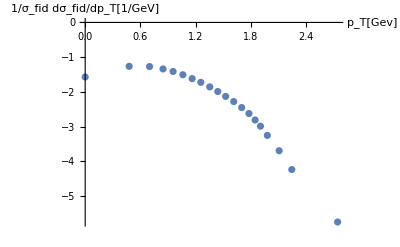

```mathematica
ErrorListPlot[ToPlot6,AxesLabel->{"p_T[Gev]", "1/σ_fid dσ_fid/dp_T[1/GeV]"},PlotRange -> All, LabelStyle->Directive[Black,FontFamily->"Helvetica",10]]
```

```mathematica
data6Export= Table[formatExport[data6[[k,i]]]//ToString,{k,1,20},{i,1,4}]
```

{{+1.000000E+00,+2.676000E-02,+2.140800E-04,+4.154269E-04},{+3.000000E+00,+5.429000E-02,+2.714500E-04,+5.150402E-04},{+5.000000E+00,+5.338000E-02,+3.202800E-04,+3.580839E-04},{+7.000000E+00,+4.567000E-02,+2.740200E-04,+3.478124E-04},{+9.000000E+00,+3.867000E-02,+2.320200E-04,+2.594062E-04},{+1.150000E+01,+3.100000E-02,+1.860000E-04,+1.807595E-04},{+1.450000E+01,+2.401000E-02,+1.680700E-04,+1.400012E-04},{+1.800000E+01,+1.877000E-02,+1.126200E-04,+9.385000E-05},{+2.250000E+01,+1.386000E-02,+9.702000E-05,+8.081699E-05},{+2.750000E+01,+1.019000E-02,+8.152000E-05,+7.348113E-05},{+3.350000E+01,+7.377000E-03,+5.163900E-05,+4.301493E-05},{+4.100000E+01,+5.226000E-03,+4.180800E-05,+3.047255E-05},{+5.000000E+01,+3.517000E-03,+2.813600E-05,+2.359275E-05},{+6.000000E+01,+2.368000E-03,+2.368000E-05,+1.707589E-05},{+7.000000E+01,+1.538000E-03,+1.999400E-05,+1.793601E-05},{+8.000000E+01,+1.021000E-03,+1.633600E-05,+1.279309E-05},{+9.500000E+01,+5.546000E-04,+7.764400E-06,+6.200617E-06},{+1.275000E+02,+2.005000E-04,+2.807000E-06,+2.064274E-06},{+1.750000E+02,+5.744000E-05,+1.493440E-06,+1.035514E-06},{+5.500000E+02,+1.765000E-06,+6.707000E-08,+4.423077E-08}}

```mathematica
(*Export["DY.newATLAS_8TeV_yrap2.0_2.4.list",data6Export,"table"]*)
```